```mathematica
(*  William Rodrigues #1  *)

f[x_]=x*Exp[-x]-1;
g[x_]=f[2.5]+D[f[2.5],x]*(x-2.5)+(1/2)*D[f[2.5],x,x]*((x-2.5)^2)+(1/3!)*D[f[2.5],x,x,x]*((x-2.5)^3);
fg=(f[x]-g[x])^2;
No=Sqrt[Integrate[fg,{x,1,4}]]
error=No*(1/3)
```

0.166371

0.055457

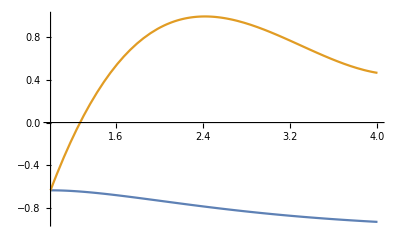

1/(2 ⅇ^4 √(210/(-203554+ⅇ (389376+ⅇ (-194052+ⅇ (-19130+ⅇ (41404+ⅇ (1425+ⅇ (-5046+ⅇ (-7327+8370 ⅇ))))))))))

1/(6 ⅇ^4 √(210/(-203554+ⅇ (389376+ⅇ (-194052+ⅇ (-19130+ⅇ (41404+ⅇ (1425+ⅇ (-5046+ⅇ (-7327+8370 ⅇ))))))))))

∞

∞

```mathematica
(*  #2  *)

f[x_]=x*Exp[-x]-1;
L1[x_]=((x-2)*(x-3)*(x-4))/((1-2)*(1-3)*(1-4));
L2[x_]=((x-1)*(x-3)*(x-4))/((2-1)*(2-3)*(2-4));
L3[x_]=((x-1)*(x-2)*(x-4))/((3-1)*(3-2)*(3-4));
L4[x_]=((x-1)*(x-3)*(x-3))/((4-1)*(4-2)*(4-3));
P[x_]=f[1]*L1[x]-f[2]*L2[x]-f[3]*L3[x]-f[4]*L4[x];
Plot[{f[x],P[x]},{x,1,4}]
fp=(f[x]-P[x])^2;
No=Sqrt[Integrate[fp,{x,1,4}]]
error=No*(1/3)

(*p is better than the cubic taylor interplant*)

fd[x_]:=D[f[x],{x,5}]
m=MaxValue[fd[x],x]
ex=(m/5!)*((4-1)^5)
```

```mathematica
(*  #3  *)

f[x_]=1/(1+x^2);
L1[x_]=((x+1)*(x)*(x-1)(x-2))/((-2+1)*(-2)*(-2-1)(-2-2));
L2[x_]=((x+2)*(x)*(x-1)(x-2))/((-1+2)*(-1)*(-1-1)(-1-2));
L3[x_]=((x+2)*(x+1)*(x-1)(x-2))/((2)*(1)*(-1)(-2));
L4[x_]=((x+2)*(x+1)*(x)(x-2))/((1+2)*(1+1)*(1)(1-2));
L5[x_]=((x+2)*(x+1)*(x)(x-1))/((2+2)*(2+1)*(2)(2-1));

P[x_]=f[-2]*L1[x]-f[-1]*L2[x]-f[0]*L3[x]-f[1]*L4[x]-f[2]*L5[x];
fP=(f[x]-P[x])^2;
No=Sqrt[Integrate[fP,{x,-2,2}]]
error=No*(1/4)
```

√(-178966/70875+(23 ArcTan[2])/3)

1/4 √(-178966/70875+(23 ArcTan[2])/3)